```mathematica
ClearAll["Global`*"]
```

```mathematica
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=1
DD[n_,z_]:=Sum[FactorialPower[z,a]/a! D2[n,a],{a,0,Log[2,n]}]
ddd[n_, z_] := (DD[n,z]-1)/z
```

```mathematica
f2[n_, a_, r_, d_] := Sum[ DD[n, r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a] + d]/(r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a] + d)/a,{t,0,a}]
f2b[n_, a_, r_, d_] := Sum[ (DD[n, r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a] + d])/( r Cos[ 2 Pi t / a ]+r I  Sin[2 Pi t / a] + d),{t,0,a}]/(2Pi r )
f2a[n_, a_, r_, d_, k_] := Sum[ DD[n, r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a] + d]/(r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a] + d)^k/a,{t,0,a}]
f3[n_,z_] := N[(DD[n,z]-1)/z]

f5[n_, a_, r_, d_] := Sum[ DD[n, E^(I t)] / (E^(I t)) * I E^(I t)* .0001,{t,0, 2 Pi, .0001}]
```

```mathematica
f2[100,10000,1.1,0]
```

28.5444-3.51927×10^-15 ⅈ

```mathematica
f3[100,0.00001]
```

28.5338

```mathematica
f5[100,1000.,1.,0]
```

1.25036×10^-7+6.28465 ⅈ

```mathematica
f4[a_, r_, d_] := Sum[ 1/(E^(t) ) * I E^(t)*.01,{t,0,2Pi,.01}]
```

```mathematica
f4[10000.,1.,0.]
```

0.+6.29 ⅈ

```mathematica
1/(2.Pi)
```

0.159155

```mathematica
Integrate[ 1/E^(I t),{t,0, 2Pi}]
```

0

```mathematica
(DD[100,1+100I]-1)/(1+100I)+(DD[100,1-100I]-1)/(1-100I)
```

583667782/9

```mathematica
ddd[100,.001]
```

1028.58

```mathematica
ddd[100,-.001]
```

-971.512

```mathematica
ddd[100,.001I]
```

28.5333-999.955 ⅈ

```mathematica
ddd[100,-1.I]
```

8.125-40.0139 ⅈ

```mathematica
Integrate[ I,{t,0, 2 Pi}]
```

2 ⅈ π

```mathematica
f2a[100,10000,1,0,4.]
```

4.25306+8.72718×10^-16 ⅈ

```mathematica
K[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
P[n_,k_]:=P[n,k]=Sum[ K[j]P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
```

```mathematica
N[P[100,4]]/24
```

4.24306

```mathematica
f4a[a_, r_, d_] := Plot[Re[(r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a] + d)/a],{t,0,a}]
f4b[a_, r_, d_] := Plot[Im[ (r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a] + d)/a],{t,0,a}]
```

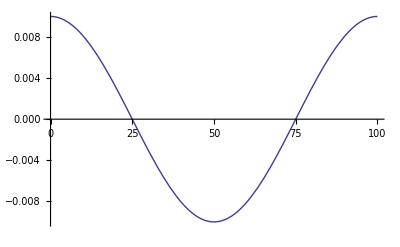

```mathematica
f4a[100,1,0]
```

```mathematica
f4c[a_, r_, d_] := Table[N[1/(r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a] + d)/a],{t,0,a}]
```

```mathematica
f4c[100,1,0]//TableForm
```

0.01
0.00998027-0.000627905 ⅈ
0.00992115-0.00125333 ⅈ
0.00982287-0.00187381 ⅈ
0.00968583-0.0024869 ⅈ
0.00951057-0.00309017 ⅈ
0.00929776-0.00368125 ⅈ
0.00904827-0.00425779 ⅈ
0.00876307-0.00481754 ⅈ
0.00844328-0.00535827 ⅈ
0.00809017-0.00587785 ⅈ
0.00770513-0.00637424 ⅈ
0.00728969-0.00684547 ⅈ
0.00684547-0.00728969 ⅈ
0.00637424-0.00770513 ⅈ
0.00587785-0.00809017 ⅈ
0.00535827-0.00844328 ⅈ
0.00481754-0.00876307 ⅈ
0.00425779-0.00904827 ⅈ
0.00368125-0.00929776 ⅈ
0.00309017-0.00951057 ⅈ
0.0024869-0.00968583 ⅈ
0.00187381-0.00982287 ⅈ
0.00125333-0.00992115 ⅈ
0.000627905-0.00998027 ⅈ
0.-0.01 ⅈ
-0.000627905-0.00998027 ⅈ
-0.00125333-0.00992115 ⅈ
-0.00187381-0.00982287 ⅈ
-0.0024869-0.00968583 ⅈ
-0.00309017-0.00951057 ⅈ
-0.00368125-0.00929776 ⅈ
-0.00425779-0.00904827 ⅈ
-0.00481754-0.00876307 ⅈ
-0.00535827-0.00844328 ⅈ
-0.00587785-0.00809017 ⅈ
-0.00637424-0.00770513 ⅈ
-0.00684547-0.00728969 ⅈ
-0.00728969-0.00684547 ⅈ
-0.00770513-0.00637424 ⅈ
-0.00809017-0.00587785 ⅈ
-0.00844328-0.00535827 ⅈ
-0.00876307-0.00481754 ⅈ
-0.00904827-0.00425779 ⅈ
-0.00929776-0.00368125 ⅈ
-0.00951057-0.00309017 ⅈ
-0.00968583-0.0024869 ⅈ
-0.00982287-0.00187381 ⅈ
-0.00992115-0.00125333 ⅈ
-0.00998027-0.000627905 ⅈ
-0.01
-0.00998027+0.000627905 ⅈ
-0.00992115+0.00125333 ⅈ
-0.00982287+0.00187381 ⅈ
-0.00968583+0.0024869 ⅈ
-0.00951057+0.00309017 ⅈ
-0.00929776+0.00368125 ⅈ
-0.00904827+0.00425779 ⅈ
-0.00876307+0.00481754 ⅈ
-0.00844328+0.00535827 ⅈ
-0.00809017+0.00587785 ⅈ
-0.00770513+0.00637424 ⅈ
-0.00728969+0.00684547 ⅈ
-0.00684547+0.00728969 ⅈ
-0.00637424+0.00770513 ⅈ
-0.00587785+0.00809017 ⅈ
-0.00535827+0.00844328 ⅈ
-0.00481754+0.00876307 ⅈ
-0.00425779+0.00904827 ⅈ
-0.00368125+0.00929776 ⅈ
-0.00309017+0.00951057 ⅈ
-0.0024869+0.00968583 ⅈ
-0.00187381+0.00982287 ⅈ
-0.00125333+0.00992115 ⅈ
-0.000627905+0.00998027 ⅈ
0.+0.01 ⅈ
0.000627905+0.00998027 ⅈ
0.00125333+0.00992115 ⅈ
0.00187381+0.00982287 ⅈ
0.0024869+0.00968583 ⅈ
0.00309017+0.00951057 ⅈ
0.00368125+0.00929776 ⅈ
0.00425779+0.00904827 ⅈ
0.00481754+0.00876307 ⅈ
0.00535827+0.00844328 ⅈ
0.00587785+0.00809017 ⅈ
0.00637424+0.00770513 ⅈ
0.00684547+0.00728969 ⅈ
0.00728969+0.00684547 ⅈ
0.00770513+0.00637424 ⅈ
0.00809017+0.00587785 ⅈ
0.00844328+0.00535827 ⅈ
0.00876307+0.00481754 ⅈ
0.00904827+0.00425779 ⅈ
0.00929776+0.00368125 ⅈ
0.00951057+0.00309017 ⅈ
0.00968583+0.0024869 ⅈ
0.00982287+0.00187381 ⅈ
0.00992115+0.00125333 ⅈ
0.00998027+0.000627905 ⅈ
0.01

```mathematica
aa=1000
Plot3D[Re[ddd[200,x+I y]],{x,-aa,aa},{y,-aa,aa}]
```

1000

```mathematica
Plot3D[Re[E^-(x+I y)],{x,-100,100},{y,-100,100}]
```

```mathematica
aa=10
Animate[Plot[Re[ddd[n,x+I]],{x,-aa,aa}],{n,530,550}]
```

10

```mathematica
aa=10
Plot3D[Im[ddd[10,x+I y]],{x,-aa,aa},{y,-aa,aa}]
```

10

```mathematica
E^(1/2. Pi I)
```

6.12323×10^-17+1. ⅈ

```mathematica
Cos[1/2. Pi] + I Sin [ 1/2. Pi ]
```

6.12323×10^-17+1. ⅈ

```mathematica
Integrate[ 1/E^(I t),{t,0,2 Pi}]
```

0

```mathematica
f2[100,100000,13.,0]
```

28.7835-1.42144×10^-13 ⅈ

```mathematica
f2[100,1000000,113.,0]
```

$Aborted

```mathematica
Integrate[ (E^(I t))^2,{t,0,Pi}]
```

0

```mathematica
D[1/z,z]
```

-1/z^2

```mathematica
f2e[n_, a_, r_] := Sum[ DD[n, r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a]]/(r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a] ),{t,0,a}]/a
```

```mathematica
f2e[100,1000,1.]
```

```mathematica
28.633333333333365+2.9920510513647967*^-16 ⅈ
```

```mathematica
f2f[n_, a_, r_] := Sum[ DD[n, r E^(2 Pi I t / a) ]/(r E^(2 Pi I t / a) ),{t,0,a}]/a
```

```mathematica
f2f[100,1000,1.]
```

28.6333+8.67639×10^-16 ⅈ

```mathematica
f2g[n_, a_, r_,d_] := Sum[ DD[n, d+r E^(2 Pi I t / a) ]/(d+r E^(2 Pi I t / a) ),{t,0,a}]/a
```

```mathematica
f2g[100,100000,.0001,0]
```

28.6336-1.19019×10^-13 ⅈ

```mathematica
f2h[n_, a_, r_,d_] := Sum[3^(d+r E^(2 Pi I t / a) )/(d+r E^(2 Pi I t / a) ),{t,0,a}]/a
```

```mathematica
f2h[100,1000000,10.,0]
```

1.10452+1.58999×10^-19 ⅈ

```mathematica
Limit[3^(z)/z,z->0]
```

∞

```mathematica
Log[3.]
```

1.09861

```mathematica
f2i[n_, a_, r_,d_] := Sum[1/(d+r E^(2 Pi I t / a) ),{t,0,a}]/a
```

```mathematica
f2i[100,100000,10.,0]
```

1.×10^-6+2.3905×10^-18 ⅈ

```mathematica
f6[n_, a_, r_, d_] := Sum[ (E^(I t))^2 / (E^(I t)-d) * I E^(I t)* .0001,{t,0, 2 Pi, .0001}]
```

```mathematica
Series[E^x/x,{x,0,20}]
```

1/x+1+x/2+x^2/6+x^3/24+x^4/120+x^5/720+x^6/5040+x^7/40320+x^8/362880+x^9/3628800+x^10/39916800+x^11/479001600+x^12/6227020800+x^13/87178291200+x^14/1307674368000+x^15/20922789888000+x^16/355687428096000+x^17/6402373705728000+x^18/121645100408832000+x^19/2432902008176640000+x^20/51090942171709440000+O[x]^21

```mathematica
f8[n_, a_, r_, d_] := Sum[ DD[n, r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a] + d]/(r Cos[ 2 Pi t / a ]+I r Sin[2 Pi t / a] + d)/a,{t,0,a}]
```

```mathematica
f8[100,1000,1.,0]
```

28.6333+5.32126×10^-16 ⅈ

```mathematica
f9[n_, a_, r_] := Sum[ DD[n, r E^(  2 Pi I t/a)] / (r E^(2 Pi I t/a)),{t,0, a}]/a
```

```mathematica
f9[100,20000., 1]
```

28.5383-2.01902×10^-15 ⅈ

```mathematica
f10[n_, a_, r_,d_] := Sum[ DD[n, d+r E^(  2 Pi I t/a)] ,{t,0, a}]/a
```

```mathematica
f10[100,20000., 1,2]
```

482.074-1.13722×10^-14 ⅈ